```mathematica
ClearAll["Global`*"]
Text["This section is to find the expressions of A and B0. First we need to find the expression of Xt"]
e[x_]:= A - B0 * α/(4 * β)* Exp[-ρ* x];
h[t_]  = Integrate[e[x], {x, 0, t}] + B
Text["Then solve for A and B given the boundary conditions"]
resAB = FullSimplify[Solve[{h[0]==0,h[T]== Q0 - B0},{A,B}]]
Text["We derive the cost formula explicitly given B0. l(x) is the cost during continuous trading phase"]
l[x_] := (B0+Ve)/2*α*Exp[-ρ*x]*e[x] + β*e[x]^2;
c[B0_] = B0^2*α + Integrate[l[x],{x,0,T}];
FullSimplify[B0^2*α + Integrate[l[x],{x,0,t}]]
A=FullSimplify[resAB[[All,1,2]]];
FullSimplify[c[B0_] ]
resB0 = Solve[D[c[B0],B0]==0,B0];
Text["B0"]
B0=FullSimplify[resB0[[All,1,2]]]
Text["A"]
A=FullSimplify[resAB[[All,1,2]]]
B=FullSimplify[resAB[[All,2,2]]];
Text["Cost of optimal"]
c1[t_] = B0^2*α + Integrate[l[x],{x,0,t}]
Text["Cost of twap"]
j[x_] := Ve/2*α*Exp[-ρ*x]*(Q0/T) + β*(Q0/T)^2;
c2[t_]=Integrate[Ve/2*α*Exp[-ρ*x]*(Q0/T) + β*(Q0/T)^2 ,{x,0,t}]
```

This section is to find the expressions of A and B0. First we need to find the expression of Xt

B+A t-(B0 (1-ⅇ^(-t ρ)) α)/(4 β ρ)

Then solve for A and B given the boundary conditions

{{A→(-4 B0+4 Q0+(B0 (1-ⅇ^(-T ρ)) α)/(β ρ))/(4 T),B→0}}

We derive the cost formula explicitly given B0. l(x) is the cost during continuous trading phase

B0^2 α+A^2 t β+(A (1-ⅇ^(-t ρ)) Ve α)/(2 ρ)-(B0 ⅇ^(-t ρ) (B0+2 Ve) α^2 Sinh[t ρ])/(16 β ρ)

{(ⅇ^(-2 T ρ) (2 (-B0 α+ⅇ^(T ρ) (B0 α+4 (-B0+Q0) β ρ)) (-(B0+2 Ve) α+ⅇ^(T ρ) ((B0+2 Ve) α+4 (-B0+Q0) β ρ))+T α ρ B0_ (α (2 Ve+B0_)-ⅇ^(2 T ρ) (2 Ve α+(α-32 β ρ) B0_))))/(32 T β ρ^2)}

B0

{(8 ⅇ^(T ρ) Q0 β ρ (α-ⅇ^(T ρ) (α-4 β ρ))+(-1+ⅇ^(T ρ)) Ve α (α (2+T ρ)+ⅇ^(T ρ) (8 β ρ+α (-2+T ρ))))/(α^2 (2+T ρ)-4 ⅇ^(T ρ) α (α-4 β ρ)+ⅇ^(2 T ρ) (2 α^2-α (T α+16 β) ρ+32 β (T α+β) ρ^2))}

A

{{(ⅇ^(-T ρ) α (4 ⅇ^(T ρ) Q0 T β ρ^2 (α-ⅇ^(2 T ρ) (α-32 β ρ))+(-1+ⅇ^(T ρ)) Ve (-α+ⅇ^(T ρ) (α-4 β ρ)) (α (2+T ρ)+ⅇ^(T ρ) (8 β ρ+α (-2+T ρ)))))/(4 T β ρ (α^2 (2+T ρ)-4 ⅇ^(T ρ) α (α-4 β ρ)+ⅇ^(2 T ρ) (2 α^2-α (T α+16 β) ρ+32 β (T α+β) ρ^2)))}}

Cost of optimal

{{(α (8 ⅇ^(T ρ) Q0 β ρ (α-ⅇ^(T ρ) (α-4 β ρ))+(-1+ⅇ^(T ρ)) Ve α (α (2+T ρ)+ⅇ^(T ρ) (8 β ρ+α (-2+T ρ))))^2)/((α^2 (2+T ρ)-4 ⅇ^(T ρ) α (α-4 β ρ)+ⅇ^(2 T ρ) (2 α^2-α (T α+16 β) ρ+32 β (T α+β) ρ^2))^2)+(α^2 (ⅇ^(-2 (t+T) ρ) (2 ⅇ^(2 t ρ) t Ve^2 α^4 (2+T ρ)^2-4 ⅇ^((t+T) ρ) T Ve^2 α^4 (2+T ρ)^2-ⅇ^(2 T ρ) T^2 Ve^2 α^4 ρ (2+T ρ)^2-8 ⅇ^(3 T ρ) T^2 Ve^2 α^3 ρ (2+T ρ) (-α+4 β ρ)+4 ⅇ^((2 t+T) ρ) t Ve α^3 (2+T ρ) (4 Q0 T β ρ^2+4 Ve β ρ (4+T ρ)-Ve α (6+T ρ))+4 ⅇ^((t+2 T) ρ) T Ve α^3 (2+T ρ) (-4 Q0 T β ρ^2-4 Ve β ρ (8+T ρ)+Ve α (10+T ρ))-4 ⅇ^(2 t ρ+5 T ρ) t Ve (32 α β ρ-32 β^2 ρ^2+α^2 (-6+T ρ)) (4 Q0 T β ρ^2 (-α+32 β ρ)+Ve (α-4 β ρ) (8 β ρ+α (-2+T ρ)))+4 ⅇ^((t+6 T) ρ) T Ve (-32 β^2 ρ^2+16 α β ρ (1-2 T ρ)+α^2 (-2+T ρ)) (4 Q0 T β ρ^2 (-α+32 β ρ)+Ve (α-4 β ρ) (8 β ρ+α (-2+T ρ)))+2 ⅇ^(2 (t+3 T) ρ) t (4 Q0 T β ρ^2 (-α+32 β ρ)+Ve (α-4 β ρ) (8 β ρ+α (-2+T ρ)))^2-8 ⅇ^(5 T ρ) T^2 α ρ (16 Q0^2 β^2 ρ^2 (α-4 β ρ)-32 Q0 Ve β^2 ρ^2 (4 β ρ+α (-1+2 T ρ))+Ve^2 (64 β^3 ρ^3+12 α^2 β ρ (2-3 T ρ)+α^3 (-2+T ρ)+16 α β^2 ρ^2 (-5+4 T ρ)))+8 ⅇ^(2 t ρ+3 T ρ) t Ve α (4 Q0 T β ρ^2 (16 β^2 ρ^2+α^2 (2-T ρ)+16 α β ρ (1+T ρ))+Ve (-96 α β^2 ρ^2 (4+T ρ)+64 β^3 ρ^3 (4+T ρ)+α^3 (-20+T^2 ρ^2)-4 α^2 β ρ (-40-6 T ρ+T^2 ρ^2)))+8 ⅇ^((t+3 T) ρ) T Ve α^2 (8 Q0 T β ρ^2 (α-4 β ρ)+Ve (-64 β^2 ρ^2 (3+T ρ)+8 α β ρ (16+T ρ-2 T^2 ρ^2)+α^2 (-20-4 T ρ+T^2 ρ^2)))-2 ⅇ^(2 (t+T) ρ) t α^2 (-16 Q0^2 T^2 β^2 ρ^4+8 Q0 T Ve β ρ^2 (-4 β ρ (4+T ρ)+α (6+T ρ))+Ve^2 (α^2 (-60-20 T ρ+T^2 ρ^2)-16 β^2 ρ^2 (24+12 T ρ+T^2 ρ^2)+8 α β ρ (40+18 T ρ+T^2 ρ^2)))-2 ⅇ^(2 (t+2 T) ρ) t (32 Q0^2 T^2 α β^2 ρ^4 (α-32 β ρ)-16 Q0 T Ve α β ρ^2 (α^2 (2+T ρ)+16 β^2 ρ^2 (15+4 T ρ)-4 α β ρ (24+5 T ρ))+Ve^2 (-1024 β^4 ρ^4+256 α β^3 ρ^3 (12+T ρ)+32 α^2 β^2 ρ^2 (-72+T^2 ρ^2)-16 α^3 β ρ (-40+6 T ρ+T^2 ρ^2)+α^4 (-60+20 T ρ+T^2 ρ^2)))-4 ⅇ^((t+5 T) ρ) T Ve (16 Q0 T α β ρ^2 (α^2-36 α β ρ+128 β^2 ρ^2)+Ve (1024 β^4 ρ^4+1024 α β^3 ρ^3 (-2+T ρ)-1152 α^2 β^2 ρ^2 (-1+T ρ)+α^4 (20-12 T ρ+T^2 ρ^2)-16 α^3 β ρ (16-17 T ρ+2 T^2 ρ^2)))+ⅇ^(6 T ρ) T^2 ρ (64 Q0^2 β^2 ρ^2 (α-4 β ρ)^2-128 Q0 Ve β^2 ρ^2 (α-4 β ρ) (4 β ρ+α (-1+4 T ρ))+Ve^2 α (512 β^3 ρ^3-α^3 (-2+T ρ)^2+64 α β^2 ρ^2 (-5+9 T ρ)+32 α^2 β ρ (2-5 T ρ+2 T^2 ρ^2)))-2 ⅇ^(4 T ρ) T^2 α^2 ρ (-32 Q0^2 β^2 ρ^2-64 Q0 Ve β^2 ρ^2+Ve^2 (32 β^2 ρ^2 (5+T ρ)+α^2 (12-T^2 ρ^2)+16 α β ρ (-6+3 T ρ+2 T^2 ρ^2)))-8 ⅇ^((t+4 T) ρ) T Ve α (4 Q0 T β ρ^3 (-T α (α-32 β ρ)+8 β (3 α+2 β ρ))+Ve (64 β^3 ρ^3 (8+T ρ)+64 α β^2 ρ^2 (-9+3 T ρ+T^2 ρ^2)+α^3 (-20+4 T ρ+T^2 ρ^2)-4 α^2 β ρ (-48+24 T ρ+5 T^2 ρ^2))))+T (-64 ⅇ^(2 T ρ) Q0^2 T β^2 ρ^3 (α-ⅇ^(T ρ) α+4 ⅇ^(T ρ) β ρ)^2+16 Q0 T Ve β ρ^2 (896 ⅇ^(4 T ρ) β^3 ρ^3+(-1+ⅇ^(T ρ))^2 (1+ⅇ^(T ρ)) α^3 (2+T ρ+ⅇ^(T ρ) (-2+T ρ))-8 ⅇ^(T ρ) (-1+ⅇ^(T ρ)) α^2 β ρ (2+ⅇ^(2 T ρ) (-9+4 T ρ)+ⅇ^(T ρ) (7+8 T ρ))+32 ⅇ^(2 T ρ) α β^2 ρ^2 (1+14 ⅇ^(T ρ)+ⅇ^(2 T ρ) (-15+28 T ρ)))+ⅇ^(-T ρ) (-1+ⅇ^(T ρ)) Ve^2 (-4096 ⅇ^(4 T ρ) β^4 ρ^4+(-1+ⅇ^(T ρ)) α^4 (4+ⅇ^(T ρ) (-4+T ρ)) (2+T ρ+ⅇ^(T ρ) (-2+T ρ))^2-512 ⅇ^(3 T ρ) α β^3 ρ^3 (8+T ρ+2 ⅇ^(T ρ) (-4+5 T ρ))-64 ⅇ^(2 T ρ) α^2 β^2 ρ^2 (8 (3+T ρ)+ⅇ^(T ρ) (-48+37 T ρ+9 T^2 ρ^2)+ⅇ^(2 T ρ) (24-45 T ρ+17 T^2 ρ^2))-16 ⅇ^(T ρ) α^3 β ρ (16+10 T ρ+T^2 ρ^2+ⅇ^(T ρ) (-48+10 T ρ+11 T^2 ρ^2)+ⅇ^(3 T ρ) (-16+30 T ρ-19 T^2 ρ^2+4 T^3 ρ^3)+ⅇ^(2 T ρ) (48-50 T ρ+7 T^2 ρ^2+4 T^3 ρ^3))))))/(32 T^2 β ρ^2 (32 ⅇ^(2 T ρ) β^2 ρ^2-(-1+ⅇ^(T ρ)) α^2 (2+T ρ+ⅇ^(T ρ) (-2+T ρ))+16 ⅇ^(T ρ) α β ρ (1+ⅇ^(T ρ) (-1+2 T ρ)))^2)}}

Cost of twap

(Q0 (2 Q0 t β+((1-ⅇ^(-t ρ)) T Ve α)/ρ))/(2 T^2)

Cost of twap

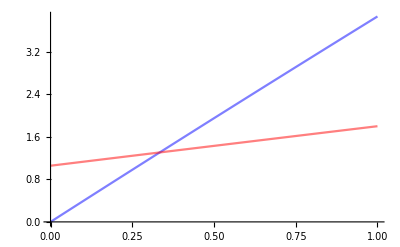

```mathematica
Ve=7707.0;
α=0.000213;
β=0.0003;
ρ=0.192886;
T=1;
Q0=10397.0;
p1=Plot[c1[t]/Q0,{t,0,T},PlotRange->Automatic,PlotStyle->Directive[Opacity[0.5],Red],AxesOrigin->{0,0}];
p2=Plot[c2[t]/Q0,{t,0,T},PlotRange->Automatic,PlotStyle->Directive[Opacity[0.5],Blue],AxesOrigin->{0,0}];
plot=Show[{p2,p1}]
```

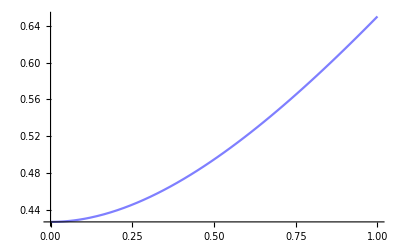

-Graphics-

```mathematica
AxesOrigin->{0,0}]
```